```mathematica
path="/Users/pp245/Desktop/goBlueFullSoftware/AcquisitionStandAlone/data/test_data_withCMSDRL.txt";
path2="/Users/pp245/Desktop/goBlueFullSoftware/AcquisitionStandAlone/data/test_data.txt";

path3="/Users/pp245/Desktop/goBlueFullSoftware/AcquisitionStandAlone/data/test_data_noCMSDRL.txt";

data1=Import[path,"Table"][[1]];
data2=Import[path2,"Table"][[1]];
data3=Import[path3,"Table"][[1]];

ListPlot[{data2-data3,data1-data3},PlotStyle->{Red,Blue,Green},Joined->True]
ListPlot[{data1-data3},PlotStyle->{Red,Blue,Green},Joined->True]
```

```mathematica
path="/Users/pp245/Desktop/goBlueFullSoftware/AcquisitionStandAlone/data/chunk_timing_test.txt";
 dat=Import[path,"Table"][[All,2]];
```

```mathematica
n=Length[dat]
n/2048.0
```

20377

9.94971

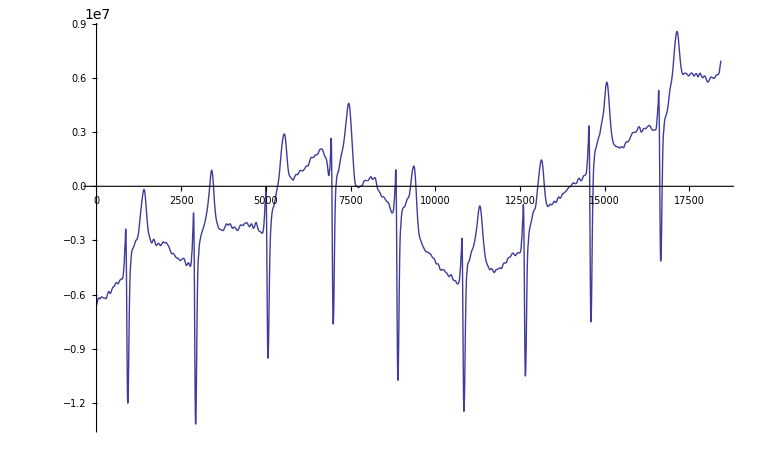

```mathematica
ListPlot[WienerFilter[Take[GaussianFilter[ dat-Mean[dat],40],9*2048],40],Joined->True,PlotRange->{}]
```

```mathematica
5300- 3800
```

1500

```mathematica
2048
```